```mathematica
ClearAll["Global`*"]
```

## N = 60

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=5
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten := 2.25 10^7
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {4.41822} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {1.08556} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {4.41822} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 2.12521×10^7.

CompiledFunction::cfse: Compiled expression {4.41822} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

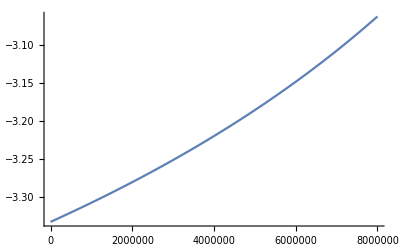

```mathematica
Plot[ϕ[t]-ϕend,{t,0,8 10^6},PlotRange->All]
```

```mathematica
tend
```

2.08678×10^7

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
ϕ[hc[0.05]]
```

4.09743

```mathematica
k:=0.00009
Timing[PS[k]]
```

{8.625,2.85011×10^-9}

```mathematica
k:=0.05
Timing[PS[k]]
```

{29.2969,2.16544×10^-9}

```mathematica
k:=0.002
Timing[r[k]]
```

{165.5,0.000704006}

## Extracting PS(k) N =60

```mathematica
list =Parallelize[Table[{k,PS[k]},{k,0.0001,0.1,0.0001}]];
list1  = Parallelize[Table[{k,PS[k]},{k,0.1+0.01,2.5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data\\k_vs_PS(k)_mu=10.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data\k_vs_PS(k)_mu=10.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PS(k) N = 60

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=5.dat","Table"]
```

```mathematica
Length[powerspectra]
```

1990

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
Length[powerspectra]
```

1990

```mathematica
fit=NonlinearModelFit[powerspectra[[;;1600]],AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot]+ β/6 (Log[k/kpivot])^2),{AS,spec, α, β},k]
```

FittedModel[2.17601×10^-9 ⅇ^(-0.175494+«22» («1»)^2) k^(-0.0583995+«23» Log[20. k]+0.000350676 Log[20. k]^2)]

```mathematica
Normal[%]
```

2.17601×10^-9 ⅇ^(-0.175494+0.00105053 Log[20. k]^2) k^(-0.0583995+0.0000606942 Log[20. k]+0.000350676 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→2.17482×10^-9,spec→0.941419,α→0.000121388,β→0.00210406}

```mathematica
PPS[k_]:=2.176008952692848*^-9 ⅇ^(-0.17549408990065804+0.0010505320041849246 Log[20. k]^2) k^(-0.05839954289379207+0.00006069417157764865 Log[20. k]+0.00035067619808983285 Log[20. k]^2)
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k] dPPS[k];
```

```mathematica
PPS[0.05]
```

2.17482×10^-9

```mathematica
nnS[0.002/0.05]
```

0.941444

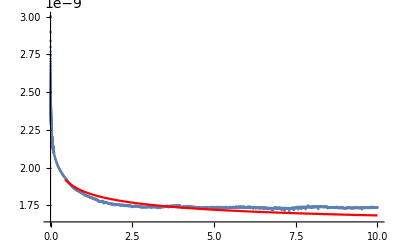

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{plot1, plot2}]
```

```mathematica
fit["RSquared"]
```

0.999955

## N = 50

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-50==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=5
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten := 1.78 10^7
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->200000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->200000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {4.41822} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {1.17832} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {4.41822} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {4.41822} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {1.87276×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.83573×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.81136×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ϕini
```

CompiledFunction::cfse: Compiled expression {1.17832} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

1.17832

```mathematica
M
```

0.00227959

```mathematica
tend
```

1.75031×10^7

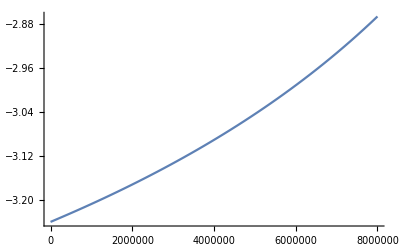

```mathematica
Plot[ϕ[t]-ϕend,{t,0,8 10^6},PlotRange->All]
```

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
ϕ[hc[0.05]]
```

1.2948

```mathematica
k:=0.00009
Timing[PS[k]]
```

{40.0313,1.80543×10^-9}

```mathematica
k:=0.05
Timing[PS[k]]
```

{108.391,1.21951×10^-9}

```mathematica
k:=0.002
Timing[r[k]]
```

{98.1094,0.00121018}

## Extracting PS(k) N =50

```mathematica
list =Parallelize[Table[{k,PS[k]},{k,0.0001,0.1,0.0001}]];
list1  = Parallelize[Table[{k,PS[k]},{k,0.1+0.01,2.5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data\\k_vs_PS(k)_mu=10.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data\k_vs_PS(k)_mu=10.dat

## Fitting PS(k) N = 50

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=5_n50.dat","Table"]
```

```mathematica
Length[powerspectra]
```

1990

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
Length[powerspectra]
```

1990

```mathematica
fit=NonlinearModelFit[powerspectra[[;;1600]],AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot]+ β/6 (Log[k/kpivot])^2),{AS,spec, α, β},k]
```

FittedModel[2.19591×10^-9 ⅇ^(-0.19266-0.0000484842 Log[20. k]^2) k^(-0.0658111-0.000500652 Log[20. k]-0.0000161844 Log[20. k]^2)]

```mathematica
Normal[%]
```

2.19591×10^-9 ⅇ^(-0.19266-0.0000484842 Log[20. k]^2) k^(-0.0658111-0.000500652 Log[20. k]-0.0000161844 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→2.20579×10^-9,spec→0.935689,α→-0.0010013,β→-0.0000971066}

```mathematica
PPS[k_]:=2.1959054827678384*^-9 ⅇ^(-0.1926595225362495-0.00004848423979684261 Log[20. k]^2) k^(-0.06581114742523647-0.0005006518352220971 Log[20. k]-0.00001618443684866514 Log[20. k]^2)
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k] dPPS[k];
```

```mathematica
PPS[0.05]
```

2.20579×10^-9

```mathematica
nnS[0.002/0.05]
```

0.93591

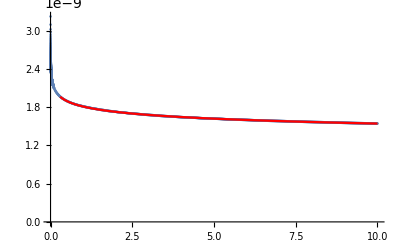

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{plot1, plot2}]
```

```mathematica
fit["RSquared"]
```

0.999997